## Simple Task 5 8am CPS/Math371 Valerie Richmond

1.

```mathematica
(*These Modules go through the numbers between the given boundary numbers and, for each, add to the resulting list a list of the number and the sum of the digits.*)
getSumDigitsList[start_,stop_] := Module[{low=start, end=stop, resList={},digitList},
While[low≤end, digitList=getList[low];AppendTo[resList, digitList];low++];Return[resList]]
```

```mathematica
(*For use in getSumDigitsList, this Module returns a list of a given number and the sum of its digits.*)
```

```mathematica
getList[number_]:=Module[{num=number,resList={}},
AppendTo[resList, num];AppendTo[resList, Total[IntegerDigits[num]]];Return[resList]]
```

```mathematica
getSumDigitsList[187,203]
```

{{187,16},{188,17},{189,18},{190,10},{191,11},{192,12},{193,13},{194,14},{195,15},{196,16},{197,17},{198,18},{199,19},{200,2},{201,3},{202,4},{203,5}}

2.

```mathematica
(*This Module shows a graph of the points in a given list. The points are joined and those with a y of 4 or 7 are yellow. The rest are red.*)
plotList[numList_]:=Module[{count, list=numList, yellowList={}, redList={}},
(*Each element in the given list is added to the appropriate list: yellow if the y is 4 or 7, and red otherwise.*)
For[count=1, count≤Length[list], count++, If[list[[count,2]]==4||list[[count,2]]==7,AppendTo[yellowList, list[[count]]], AppendTo[redList, list[[count]]] ] ];
(*The lists are shown with their characteristic colors, sizes, and connections.*)
Show[ListPlot[{list,yellowList, redList},Joined->{True, False, False}, PlotStyle->{Directive[Green], Directive[Yellow, PointSize-> 0.035], Directive[Red,PointSize->.025]}]]]
```

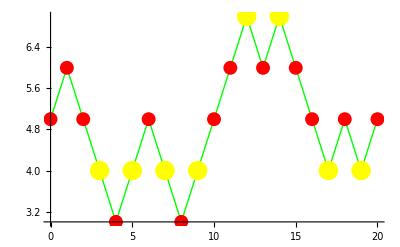

```mathematica
ST5lst={{0,5},{1,6},{2,5},{3,4},{4,3},{5,4},{6,5},{7,4},{8,3},{9,4},{10,5},{11,6},{12,7},{13,6},{14,7},{15,6},{16,5},{17,4},{18,5},{19,4},{20,5}};

plotList[ST5lst]
```